```mathematica
(* Gradient Descent with Modification *)

(* Fitting Function *)
Fitfunction=#2*Exp[#1*#3]+#4&;
varamt=3;

(* Data Generation Settings *)
ParamVariance=3;
DataLength=100;
SamplingRate=10;
SamplingSet=N[Range[DataLength]]/N[SamplingRate];
NoiseDistribution=NormalDistribution[];
manualTrueParams={1.,-2.,2.};
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];

(* Data Generation *)
DataNoiseless=(Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet);
NoiseMagnitude=Variance[DataNoiseless]*0.3;
Noise[x_]:=x*(1.+NoiseMagnitude*RandomVariate[NoiseDistribution]);
Data=Noise/@DataNoiseless;

(*Prep gradient*)
Clear[eFunc,gFunc,params]
params=Table[Unique["p"],{varamt}];
paramh=Hold@@params;
oFunc=paramh/._[vars__]:>Function[{vars},N[Mean[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]/DataLength]];
eFunc=paramh/._[vars__]:>Function[{vars},N[Mean[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[oFunc@@params,params]];
```

```mathematica
(*** Iteration Initialization ***)
factor=0.01;
totalIter=0;
TotalRefines=0;
AccelBoost=1.;
AccelRefine=1.;
dirs=ConstantArray[ConstantArray[0,varamt],Smoothness];
dirX=0;
err=10000;(*Initialization of error. Start impossible.*)
prevErr=-1;

(*History*)
manualParams={-2.,1.,-2.};
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams=If[historyLength>0,ConstantArray[iterParams,historyLength],{iterParams}];
```

```mathematica
(*** Iteration Settings ***)

(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;doPoint=False;doGraph=False;fps=0;doWarn=False;
doPlot=True;doSpace=True;doEPlot=False;

(*Init*)
dir=gFunc@@iterParams;
err=eFunc@@iterParams;

(** Controls for limiting values **)
errorRatio=1.0;(*In what ratio of current error to previous error should it be considered increasing*)
boostRatio=1.1; (*'Impatience' Multiplier to increase factor when error is not increasing*)
refineRatio=0.95;(*'Caution' Multiplier to decrease factor when error is increasing*)
maxRefines=1000;(*Give up refining if refined too many times in a row*)
Smoothness=2;
AccelAmt=0.01;
coolCoeff=2.;
coolRate=2.;

(* Tunneling values *)
TunnelingNormThreshold=1.0*10^-5;
TunnelingGrowthRate=5;
TunnelingBailout=100;

(* Tracker values *)
ConsecRefines=0;
historyLength=0;
historyLengthi=0;
historyAmt=100;

(* Iteration Tools Extracted for Compactness *)
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nnorm:",norm,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
```

```mathematica
(* Realtime monitor plot *)
displayGradient[xV_,yV_]:=Show[
ContourPlot[eFunc @@ ReplacePart[iterParams, {xV->x,yV->y}],
{x,iterParams[[xV]]-0.2,iterParams[[xV]]+0.2},{y,iterParams[[yV]]-0.2,iterParams[[yV]]+0.2},
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
(* Visualization of the first 3 function parameters *)
Dynamic[Grid[{{"Data vs Function","Parameter Space","Error over iterations"},
{ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium,PlotLegends->None]
,If[doPoint,If[varamt==3,If[doGraph,
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]},
Show[ListPointPlot3D[If[historyAmt>0&&totalIter>historyAmt,debugParams[[-historyAmt;;-1]],debugParams],PlotRange->All,ImageSize->Medium],Graphics3D@Line@debugParams]],
"Non-3 dimensions"],
"Disabled"],
If[doEPlot,ListLogPlot[{((eFunc@@#)&)/@debugParams},ImageSize->Medium],"Disabled"]
},
{"Parameters, nGrad, dir, Delta","Iterations, factor, corrections"},{Column[{iterParams,-dir,-factor*dir,-factor*Mean[dirs]}],Column[{{totalIter,factor,TotalRefines},ProgressIndicator[ConsecRefines/maxRefines]}],{err,prevErr}}
},Frame->All,ItemSize->30]]
```

```mathematica
(*** Iteration loop ***)
(* Iterator and maximum values *)
i=0.;UpperBound=1400.;SmallErr=0.0000000000000001;
Forever=True;
ConsecRefines=0;
err=eFunc @@ iterParams;
(* Iteration *)
While[Forever||(i<UpperBound && ((err(err-prevErr))^2+1)^2>(1+SmallErr)),
dirX=Mod[++dirX,Smoothness];
dirs[[dirX+1]]=dir=gFunc @@ iterParams;
If[ConsecRefines==0,i++;totalIter++;];
prevErr=err;
err=eFunc @@ iterParams;
If[Log10[factor]<-100,factor=0.5];
factor*=boostRatio^AccelBoost;ConsecRefines=0;AccelBoost+=AccelAmt;AccelRefine=1.;
(*Line search*)
While[(eFunc@@(iterParams-factor*Mean[dirs]))/prevErr>errorRatio,
If[ConsecRefines>maxRefines,Abort[]];
factor*=refineRatio^AccelRefine;ConsecRefines++;TotalRefines++;AccelRefine+=AccelAmt;AccelBoost=1.;
];
iterParams-=factor*Mean[dirs];
ReportIteration[i];
If[fps≠0&&ConsecRefines==0,Pause[fps];];(*Pause*)
If[historyLength>0,
historyLengthi=Mod[++historyLengthi,historyLength];
debugParams[[historyLengthi+1]]=iterParams,
debugParams=Append[debugParams,iterParams];
];
]
```

$Aborted

{0.986845,-1.90951,2.04442}

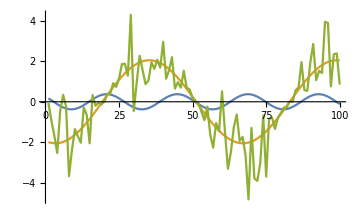

2.32124×10^-8

```mathematica
(***Diagnostic Tools***)

(*Optional Noise Function Plot*)
Plot[Noise[x],{x,0,40},AspectRatio->Full,ColorFunction->Function[{x,y},Hue[Abs[y-x]]]];

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]]

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium]

Norm[dir]
```

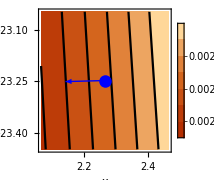
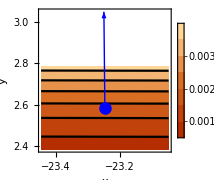
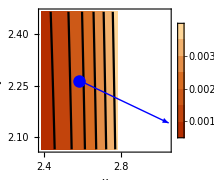

```mathematica
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]}
```

```mathematica
factor=0.05
```

0.05

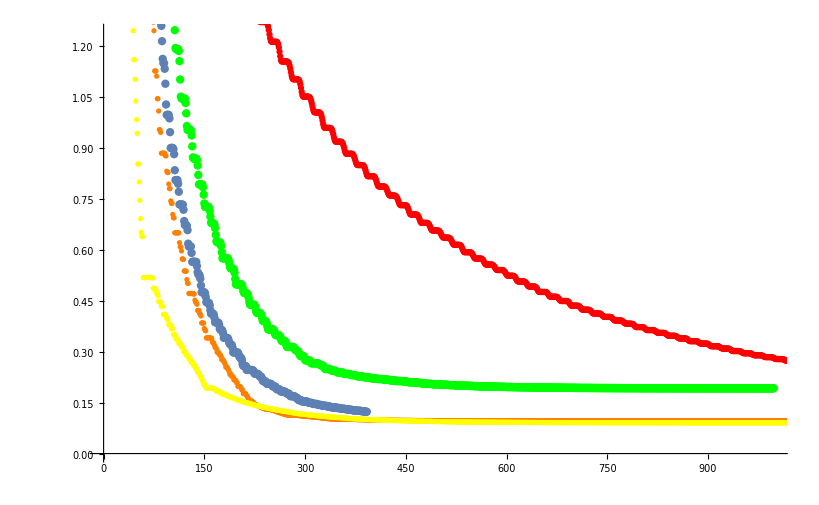

```mathematica
sm2=ListPlot[((eFunc @@ #)&)/@debugParams,PlotStyle->Yellow];
Show[{sm12,sm16,sm4,sm8,sm2},Range->All]
```

```mathematica
ListPointPlot3D[debugParams]
```

-Graphics3D-

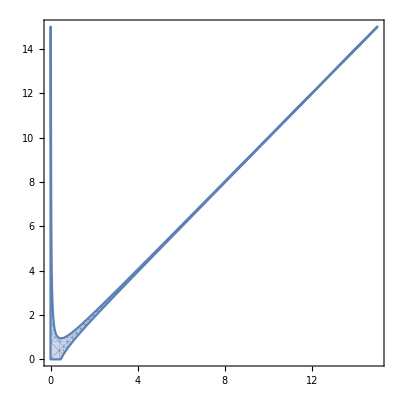

```mathematica
RegionPlot[((x(x-y))^2+1)^2<1.1,{x,0,15},{y,0,15}]
```

```mathematica
Variance[dir]/Norm[dir]
```

0.0000517737